# cavity misalignment

P. Huft

A notebook for calculating the effects of misalignment on near-concentric cavity.

```mathematica
nm=10^-9;
um=10^-6;
mm=10^-3;
mrad=10^-3;
```

## effects from tilt

Evaluate the subsections below in order.

### scattering loss

The expressions which compute the critical distance for the tilted cavity mode might be incorrect. Check them against the ones that Louis Farenci and I derived, in my cavity alignment jupyter notebook.

Assume one mirror is tilted about an axis perpendicular to the optical axis and bisecting its surface. The axis of the supported cavity mode tilts as well (a nice diagram in Stamper-Kurn Julian thesis) and if it is severe there can be diffractive loss from scattering off the edge of a mirror. Below is an approximate calculation of this (algebra in my orange Rhodia dot pad).

```mathematica
λ=780 nm;
d=10 um;(*d critical*)
R=2mm;//N
L=2R-d;(*cavity length*)
r=0.5 mm(*clear aperture radius*)
"cavity params R, C.A. radius [mm]"
{R,r}/mm//N
"tilt [mrad]"
θ=.1 mrad;(*mirror tilt, rad.*)
θ /mrad//N
dx=R (Cos[θ]-1)+d;
dz=R Sin[θ];
α=ArcTan[dx,dz];(*mode tilt*)
dtilt=√(dx^2+dz^2);
"critical distance [μm] with/without tilt"
{dtilt,d}/um//N
Ltilt =2R-dtilt;(*cav length with tilt*)
"cavity mode waist [μm], with/without tilt"
w0=√((λ L)/(2 π))((R-L/2)/(L/2))^(1/4);
w0tilt=√((λ L)/(2 π))((R-Ltilt/2)/(Ltilt/2))^(1/4);
{w0,w0tilt}/um//N
zR=π w0^2/λ;(*Rayleigh range*)
zRtilt =π w0tilt^2/λ
(*cav waist with tilt*)
"mode waist at mirror [μm], with/without tilt"
wMtilt=w0tilt(1+((2R-dtilt)/(2 zR))^2)^(1/2);
wM=w0tilt(1+((2R-d)/(2 zRtilt))^2)^(1/2);
{wMtilt,wM}/um//N
(*Clear[θ,d,L,R,r,α,w];*)
"displacement of mode on mirror [mm]"
x0=R Sin[θ];(*this is not quite correct*)
x0/mm//N
mode=Exp[-(2 ((x-x0)^2+y^2))/wMtilt^2];(*mode on the mirror*)
"ppm diffractive loss per side"
ppmLoss=10^6(1-Integrate[mode,{x,-r,r},{y,-√(r^2-x^2),√(r^2-x^2)}]/(2π Integrate[Exp[-2 ρ^2/wM^2]ρ,{ρ,0,∞}]))//N
```

0.0005

cavity params R, C.A. radius [mm]

{2.,0.5}

tilt [mrad]

0.1

critical distance [μm] with/without tilt

{10.002,10.}

cavity mode waist [μm], with/without tilt

{4.97967,4.97992}

mode waist at mirror [μm], with/without tilt

{99.3493,99.3494}

displacement of mode on mirror [mm]

0.039992

ppm diffractive loss per side

0.997389

Generate a table of values.

```mathematica
tiltTable={2,1.5,1.2,1.1,1.05,1,0.7,0.5,0.1,0.05,0.01,0.005,0.001}mrad(*Table[10^-i mrad,{i,Range[0,4]}]*);
lossTable={};
Clear[θ];
For[i=1,i<Length[tiltTable]+1,i++,
(*mirror tilt, rad.*)
θ=tiltTable[[i]];
dx=R (Cos[θ]-1)+d;
dz=R Sin[θ];
α=ArcTan[dx,dz];(*mode tilt*)
dtilt=√(dx^2+dz^2);
Ltilt =2R-dtilt;(*cav length with tilt*)
w0=√((λ L)/(2 π))((R-L/2)/(L/2))^(1/4);
w0tilt=√((λ L)/(2 π))((R-Ltilt/2)/(Ltilt/2))^(1/4);
zR=π w0^2/λ;(*Rayleigh range*)
(*cav waist with tilt*)
wMtilt=w0tilt(1+((L-dtilt)/(2 zR))^2)^(1/2);
wM=w0tilt(1+((L-d)/(2 zR))^2)^(1/2);
x0=R Sin[α];
mode=Exp[-(2 ((x-x0)^2+y^2))/wMtilt^2];(*mode on the mirror*)
AppendTo[lossTable,10^6(1-Integrate[mode,{x,-r,r},{y,-√(r^2-x^2),√(r^2-x^2)}]/(2π Integrate[Exp[-2 ρ^2/wM^2]ρ,{ρ,0,∞}]))//N];
]
(*ppmTable=Array[10^6 Integrate[mode,{x,-r,r},{y,-√(r^2-x^2),√(r^2-x^2)}]/(2π Integrate[Exp[-2 ρ^2/wM^2]ρ,{ρ,0,∞}])/.θ->tiltTable[[#]]&,tiltTable//Length]//N;*)
```

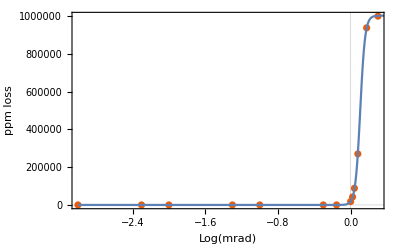

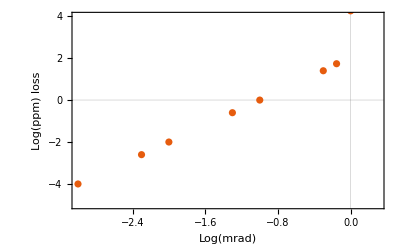

```mathematica
model=a/(1+Exp[-b (x-c)]);
fit=FindFit[Transpose@{Log10[tiltTable/mrad],lossTable},model,{a,b,c},x];
Show[ListPlot[Transpose@{Log10[tiltTable/mrad],lossTable},PlotTheme->"Scientific",FrameLabel->{"Log(mrad)","ppm loss"},PlotRange->All],
Plot[model/.fit,{x,-3,2}]]
(*the fit is only valid on a larger scale*)
Show[ListPlot[Transpose@{Log10[tiltTable/mrad],Log10[lossTable]},PlotTheme->"Scientific",FrameLabel->{"Log(mrad)","Log(ppm) loss"},PlotRange->{-5,4}]
(*,Plot[model/.fit,{x,-3,2}]*)]
```

### mode matching effect from tilt

To-do: 
* rough - estimate mode-matching by assuming a Gaussian beam starting at one mirror surface (on-center) and take the overlap with the tilted mode at that surface
* more rigorous - compute the overlap of the L.G. eigenmodes given a TEM00 mode input at one of the cavity mirrors. How does the overlap with the TEM00 go down if a mirror is tilted? This represents the situation in which the mode matching optics and cavity mirror for one side have been glued down (assumed perfectly) and the light is input through those, while the other mirror is free and being aligned.

### visualization of mode tilt for a given mirror misalignment

My expressions for the actual tilt and offset of the cavity mode and how the mode moves with given mirror misalignments are in python, in my cavity misalignment ipynb.

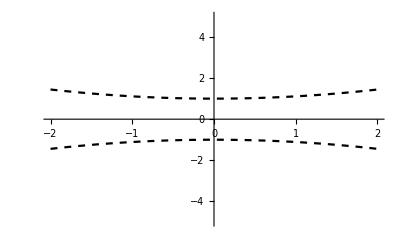

```mathematica
w0=1;
zR=3;
Plot[{w0^2(1+z^2/zR^2),-w0^2(1+z^2/zR^2)},{z,-2,2},PlotStyle->Directive[Dashed,Black],PlotRange->{-5,5}]
```

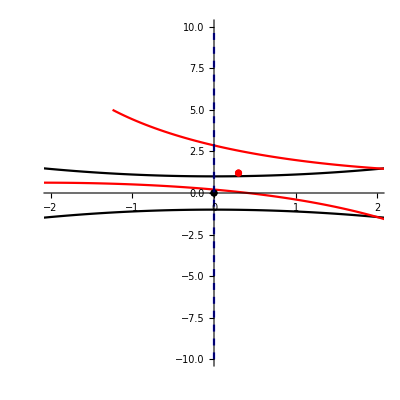

```mathematica
zpts=Range[-6,6,0.1];
wpts1=w0^2(1+z^2/zR^2)/.z->zpts;
wpts2=-w0^2(1+z^2/zR^2)/.z->zpts;
Clear[θ];
θ=0;
{wpts1Tilt,zptsTilt1}=RotationMatrix[θ].{wpts1,zpts};
{wpts2Tilt,zptsTilt2}=RotationMatrix[θ].{wpts2,zpts};
aligned=ListPlot[{Transpose@{zptsTilt1,wpts1Tilt},Transpose@{zptsTilt2,wpts2Tilt}},Joined->True,PlotStyle->Directive[Black],PlotRange->{{-2,2},{-10,10}},AspectRatio->1];
Clear[θ];
θ=0.5;(*mode tilt, presumably due to some mirror tilt or decenter*)
dx=1.2;(*mode decenter, presumably due to some mirror tilt or decenter*)
dz=0.3;(*mode tilt, presumably due to some mirror tilt or decenter*)
{wpts1Tilt,zptsTilt1}=RotationMatrix[θ].{wpts1+dx,zpts+dz};
{wpts2Tilt,zptsTilt2}=RotationMatrix[θ].{wpts2+dx,zpts+dz};
misaligned=ListPlot[{Transpose@{zptsTilt1,wpts1Tilt},Transpose@{zptsTilt2,wpts2Tilt}},Joined->True,PlotStyle->Directive[Red],PlotRange->{{-2,2},{-5,5}},AspectRatio->1];
alignedOrigin=ListPlot[{{0,0}},PlotStyle->Directive[Black]];
misalignedOrigin=ListPlot[{{dz,dx}},PlotStyle->Directive[Red]];
Show[aligned,misaligned,alignedOrigin,misalignedOrigin,ListPlot[{{0,-10},{0,10}},Joined->True,PlotStyle->Directive[Blue,Dashed]]]
```

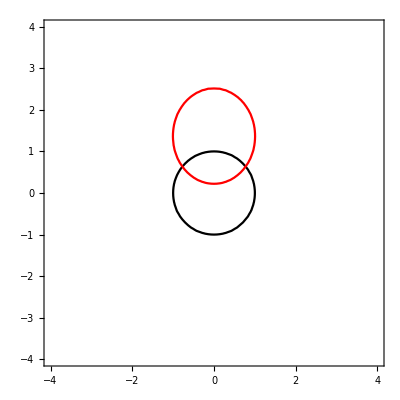

```mathematica
Show[ContourPlot[Exp[(-2 x^2)/w0^2]Exp[(-2 y^2)/w0^2]==1/ⅇ^2,{x,-4,4},{y,-4,4},ContourStyle->Black],ContourPlot[Exp[(-2(x Cos[θ]-dx)^2)/(w0^2(1+(-dz)^2/zR^2))]Exp[(-2 y^2)/(w0^2(1+(-dz)^2/zR^2))]==1/ⅇ^2,{y,-4,4},{x,-4,4},ContourStyle->Red]]
```

## tests

```mathematica
w0=1;
r=2w0;
x0=0.1;
NIntegrate[Exp[-2((x-x0)^2+y^2)/w0^2],{x,-r,r},{y,-√(r^2-x^2),√(r^2-x^2)}]/(2π NIntegrate[Exp[-2 ρ^2/w0^2]ρ,{ρ,0,∞}])
```

0.999609

```mathematica
w0=1;
r=2w0;
NIntegrate[Exp[-2 ρ^2/w0^2]ρ,{ρ,0,r}]/NIntegrate[Exp[-2 ρ^2/w0^2]ρ,{ρ,0,∞}]
```

0.999665

```mathematica
λ=7.8*^-7;
zR=(π w0^2)/λ;
RoC=2*^-3;
L=2RoC;
w0=5*10^-6;
"waist mm"
w=w0 √(1+(L/(2zR))^2);
w/mm
"clear aperture radius"
3*w/mm
```

waist mm

0.0994385

clear aperture radius

0.298315

```mathematica
zR/mm
```

0.100692